```mathematica
CloseKernels[]
```

{KernelObject[13,local,<defunct>],KernelObject[14,local,<defunct>],KernelObject[15,local,<defunct>],KernelObject[16,local,<defunct>]}

```mathematica
LaunchKernels[]
```

{KernelObject[17,local],KernelObject[18,local],KernelObject[19,local],KernelObject[20,local]}

```mathematica
e=1;
m=6;
P=2^m;
Ep=1000;
Dynamic[{Ep,e,t}]
```

```mathematica
ParallelTable[(Label[New];
n1=1;"$ player";
n2=1;"MG player";
n3=99;"Back ground";
n=n1+n2+n3;
T=20P-1;"odd steps needs";
mu=Table[0,{i,1,T}];
normalize=1/(√n);
S=2;
t=3;
mu⟦1⟧=RandomInteger[P-1];
mu⟦2⟧=RandomInteger[P-1];
signal=0;
"bestStrategy⟦i⟧,U⟦i,s⟧";"Side⟦i,bestStrategy⟦i⟧,mu⟧-->From book";
"StategySpace-->we don't construck it";
"Action=List[IntegerDigits[StrategyPosition=RandomInteger[{0,2^(2^m)-1}],2,4]]";
"AgentStrategy⟦i,s⟧--> i^thagents and the s^th strategy";
PayoffFunction=Table[0,{i,1,n},{s,1,S}];
A=Table[0,{i,1,T}];
bestStrategy=Table[0,{i,1,n},{j,1,2}];"bestStrategy⟦Fresh,React⟧";
BS=Table[0,{i,1,n},{j,1,2}];
U=Table[1,{i,1,n},{i,1,S}];
Price=Table[0,{i,1,T}];
Price⟦2⟧=Price⟦1⟧=100;"Resource level {C_i(0),n_i(0)}={n*p(0),n-1},n=10";
c=Table[10*Price⟦1⟧,{i,1,n}];
NStock=Table[0,{i,1,n},{i,1,2}];
W=Table[10*Price⟦1⟧,{i,1,n}];
AgentStrategy=Table[0,{i,1,n},{i,1,S}];
"initial set";
AgentStrategy=Table[RandomChoice[{1,-1}],{n},{S},{P}];
Do[AgentStrategy⟦i,s⟧=AgentStrategy⟦1,s⟧,{s,1,S},{i,2,n1+n2}];
Do[bestStrategy⟦i,1⟧=RandomChoice[Select[Table[If[U⟦i,s⟧≥Max[U⟦i⟧],AgentStrategy⟦i,s⟧],{s,1,S}],ListQ]],{i,1,n}];
Do[bestStrategy⟦i,2⟧=bestStrategy⟦i,1⟧,{i,1,n}];
Do[BS⟦i,1⟧=Table[-bestStrategy⟦i,2⟧⟦mu⟦t-1⟧+1⟧,{k,1,P}],{i,1,n1}];
Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,n1,n}];
Label[begin];
"Nature choice";
mu⟦t⟧=RandomInteger[P-1];
"mu⟦t⟧=Mod[2*mu⟦t-1⟧+signal,P]";
"group I,II  Agents choice s_i^*(t)=argmax{U_(i, s)(t)}  ,sent order";
Do[bestStrategy⟦i,2⟧=bestStrategy⟦i,1⟧,{i,1,n}];
Do[BS⟦i,2⟧=BS⟦i,1⟧,{i,1,n}];
Do[bestStrategy⟦i,1⟧=RandomChoice[Select[Table[If[U⟦i,s⟧≥Max[U⟦i⟧],AgentStrategy⟦i,s⟧],{s,1,S}],ListQ]],{i,1,n}];
If[OddQ[t],Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,1,n1}];,
Do[BS⟦i,1⟧=Table[-bestStrategy⟦i,2⟧⟦mu⟦t-1⟧+1⟧,{k,1,P}],{i,1,n1}]];
Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,n1+1,n}];
"Market interaction A(t)=Σ_(i = 1)^na_(i, s*)(t)
Market Maker n_M(t)=-Σ_(t = 3)^(t - 1)A(t)";
MarketAction=0;
Do[MarketAction=MarketAction+BS⟦i,1⟧⟦mu⟦t⟧+1⟧,{i,1,n}];
A⟦t⟧=MarketAction;
"signal=UnitStep[MarketAction]";
"Price/Cash/Wealth update deal t+1 ";
Price⟦t⟧=Price⟦t-1⟧+normalize*(A⟦t-1⟧);
If[t==3,
Do[W⟦i⟧=10*Price⟦1⟧,{i,1,n}];
Do[c⟦i⟧=10*Price⟦1⟧,{i,1,n}];
Do[NStock⟦i,2⟧=0,{i,1,n}];,Do[c⟦i⟧=c⟦i⟧-BS⟦i,2⟧⟦mu⟦t-1⟧+1⟧(Price⟦t⟧);W⟦i⟧=W⟦i⟧+NStock⟦i,1⟧*(Price⟦t⟧-Price⟦t-1⟧);
c⟦i⟧=N[c⟦i⟧],{i,1,n}];
Do[NStock⟦i,1⟧=NStock⟦i,2⟧;
NStock⟦i,2⟧=NStock⟦i,1⟧+BS⟦i,2⟧⟦mu⟦t-1⟧+1⟧,{i,1,n}];];
"Agents learning Payoff g_(i, s)(t)=0,odd,g_(i, s)(t)=a_(i, s)(t-1)A(t),even g_(i, s)(t)=-a_(i, s)(t)A(t)";
If[OddQ[t],Do[PayoffFunction⟦i,s⟧=0,{s,1,S},{i,1,n1}];,
Do[PayoffFunction⟦i,s⟧=(AgentStrategy⟦i,s⟧⟦mu⟦t-1⟧+1⟧)(A⟦t⟧),{s,1,S},{i,1,n1}];];
Do[PayoffFunction⟦i,s⟧=-(AgentStrategy⟦i,s⟧⟦mu⟦t⟧+1⟧)(A⟦t⟧),{s,1,S},{i,n1+1,n}];
Do[U⟦i,s⟧=U⟦i,s⟧+PayoffFunction⟦i,s⟧,{s,1,S},{i,1,n}];
t=t+1;
"Go on or Stop";
If[t>T,Goto[sample],Goto[begin]];
Label[sample];
N[{W⟦1⟧,W⟦2⟧,Mean[W⟦1;;n⟧],Price⟦T⟧}]),{e,1,Ep}]//AbsoluteTiming
```

```mathematica
Export["C:\\Users\\Jack\\Desktop\\LabWork\\final\\openm6s2p100T1279.txt",Compress[re⟦2⟧]]
```

C:\Users\Jack\Desktop\LabWork\final\openm6s2p100T1279.txt

```mathematica
Walll=Uncompress[ReadList["C:\\Users\\Jack\\Desktop\\LabWork\\final\\openm6s2p100T1279.txt",String]⟦1⟧];
```

```mathematica
Walll⟦All,4⟧;
```

```mathematica
Length[Position[Walll⟦All,4⟧,_?Negative]]
```

24

```mathematica
Wall=Table[Delete[Walll⟦All,k⟧,Position[Walll⟦All,4⟧,_?Negative]],{k,1,4}];
```

```mathematica
Dimensions[Wall]
```

{4,976}

```mathematica
Wall⟦1⟧;
```

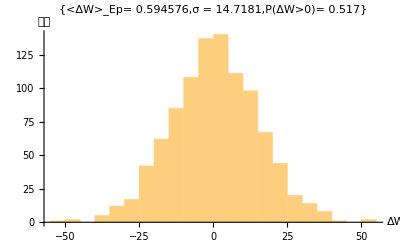

```mathematica
Histogram[Wall⟦1⟧-1000,AxesLabel->{ΔW,次數},PlotLabel->{ "<ΔW>_Ep= "<>ToString[N[Mean[Wall⟦1⟧-1000]]],"σ = "<>ToString[N[StandardDeviation[Wall⟦1⟧-1000]]],"P(ΔW>0)= "<>ToString[N[1/(Ep-Length[Position[Walll⟦All,4⟧,_?Negative]])Total[UnitStep[Wall⟦1⟧-1000]],3]]}]
```

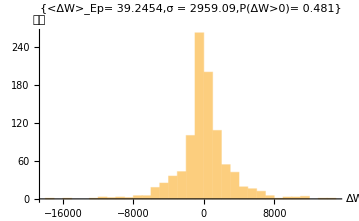

```mathematica
Histogram[Wall⟦2⟧-1000,AxesLabel->{ΔW,次數},PlotLabel->{ "<ΔW>_Ep= "<>ToString[N[Mean[Wall⟦2⟧-1000]]],"σ = "<>ToString[N[StandardDeviation[Wall⟦2⟧-1000]]],"P(ΔW>0)= "<>ToString[N[1/(Ep-Length[Position[Walll⟦All,4⟧,_?Negative]])Total[UnitStep[Wall⟦2⟧-1000]],3]]}]
```

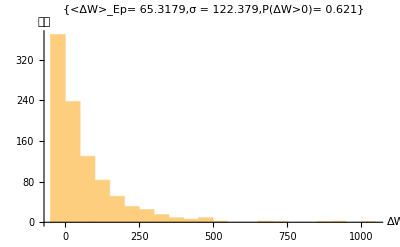

```mathematica
Histogram[Wall⟦3⟧-1000,{50},AxesLabel->{ΔW,次數},PlotLabel->{ "<ΔW>_Ep= "<>ToString[N[Mean[Wall⟦3⟧-1000]]],"σ = "<>ToString[N[StandardDeviation[Wall⟦3⟧-1000]]],"P(ΔW>0)= "<>ToString[N[1/(Ep-Length[Position[Walll⟦All,4⟧,_?Negative]])Total[UnitStep[Wall⟦3⟧-1000]],3]]}]
```

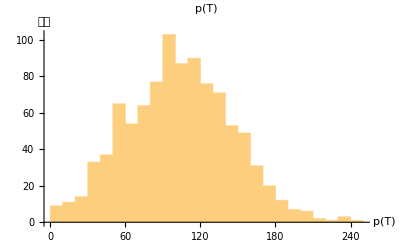

```mathematica
Histogram[Wall⟦4⟧,AxesLabel->{"p(T)",次數},PlotLabel-> "p(T)"]
```